# Diversity at the United World College

Exploring Equality and Inequality in International Schools.

Katja Della Libera, Jun. 29,  2018

The United World Colleges (UWC) are a group of currently 17 schools and National committees in 154 countries all around the world providing these high schools with the majority of their students. Initially founded in 1962 in Wales by German pedagogue Kurt Hahn, UWC aims to “make education a force to unite people, nations and cultures for peace and a sustainable future” (UWC Mission Statement). UWC tries to achieve this through several means, one important one being the diversity of the movement. In the following exploration, I will attempt to illustrate and measure diversity of UWC.

## How to measure diversity?

Diversity is hard to define and harder to measure holistically. I will therefore concentrate on the dimension of countries that is available to me in two datasets, one generated myself and containing data on the 17 UWCs, one kindly provided by the international office of UWC, dealing with the students sent to UWCs in the last three years.

Import the two Datasets:

```mathematica
schoolData=SortBy[SemanticImport[FileNameJoin[{NotebookDirectory[],"SchoolData.csv"}]],"UWC since"]
```

Dataset[<>]

```mathematica
studentData = SemanticImport[FileNameJoin[{NotebookDirectory[],"IBDP students by country (3) .csv"}]]
```

Dataset[<>]

```mathematica
studentDataArray=Import[FileNameJoin[{NotebookDirectory[],"IBDP students by country (3) .csv"}],"TSV"][[2;;]];
```

## Diversity in School Locations

Where do UWC students go to school?

UWC aims to spread their schools as much across the globe as possible.

The first thing I want to do with the school data is making it easier to read. Below, for example, the Bar Chart makes it a lot easier to see how different in scale UWC South East Asia is to all the other UWC, because they serve a large number of local Singaporean students especially in the lower years.

Make a Chart showing the number of students attending each UWC:

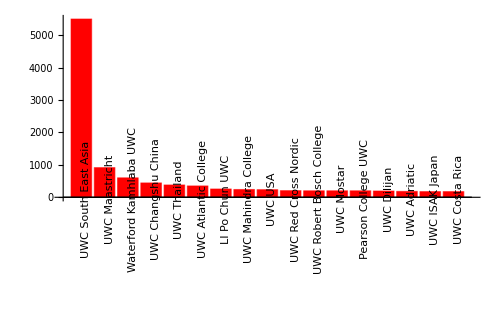

```mathematica
BarChart[ReverseSort[Map[Labeled[#[[2]],Rotate[#[[1]],Pi/2]]&,Normal[schoolData[All,{1,5}]]]],ImageSize->500,ChartStyle->Red]
```

Another interesting plot to make is the geographical locations of different UWC schools around the world. Take some time to play around with the year in the interactive graph below to see how the UWCs spread around the world over time.

The graph shows, that there is a large concentration of UWC schools in Europe . Most other UWCs are more separated, with significant gaps in Africa, Central Eurasia and South America.

Create a dataset with the Positions of the different schools.

```mathematica
Iconize[positionData={{GeoPosition[{51.437766749999,-3.3673909958136754}],"UWC Atlantic College",1962},{GeoPosition[{47.99,7.8500000000000005}],"UWC Robert Bosch College",2014},{GeoPosition[{9.94,-84.18}],"UWC Costa Rica",2006},{GeoPosition[{18.53,73.84}],"UWC Mahindra College",1997},{GeoPosition[{61.3175,5.36167}],"UWC Red Cross Nordic",1995},{GeoPosition[{50.85,5.69}],"UWC Maastricht",2009},{GeoPosition[{36.36667,138.61667}],"UWC ISAK Japan",2017},{GeoPosition[{1.3,103.85}],"UWC South East Asia",1975},{GeoPosition[{45.77914547369006,13.654813976555513}],"UWC Adriatic",1982},{GeoPosition[{43.34,17.81}],"UWC Mostar",2006},{GeoPosition[{22.284,114.15}],"Li Po Chun UWC",1992},{GeoPosition[{35.6014199,-105.2214355}],"UWC USA",1982},{GeoPosition[{7.88,98.38}],"UWC Thailand",2016},{GeoPosition[{-26.32,31.14}],"Waterford Kamhlaba UWC",1981},{GeoPosition[{48.43,-123.37}],"Pearson College UWC",1974},{GeoPosition[{40.75,44.87}],"UWC Dilijan",2014},{GeoPosition[{31.65,120.733333}],"UWC Changshu China",2015}}]
```

Make a plot of UWC school locations:

```mathematica
ListAnimate[Table[GeoListPlot[Map[Labeled[#[[1]],#[[2]]]&,Select[positionData,#[[3]]≤  y&]],GeoBackground->"CountryBorders",ImageSize->800,GeoRange->"World",PlotLabel->y],{y,1962,2018,1}],AnimationRate->1]
```

## Student Origin

Diversity in student’s country of origin:

Some of the UWC schools serve students for more than the two years of the International Baccalaureate Diploma Programme (IBDP), but those two years are the most essential, since they are the students selected by National Committees, most fulfilling the mission of UWC. So how is UWC doing in different measures of the diversity of student origin?

One interesting thing to do with this data is looking at the coverage of the national committees. As seen in the map below, UWC selects students from almost every country, gaps exist only in the Sahara region (which already has low population density) and in other countries like North Korea. Some of these have small population numbers, randomizing the question whether there is a UWC student from the given country, others have political issues that may misalign them with UWC' s values.

Make a map of countries from which students attend UWC, point at a country to see it’s name:

```mathematica
GeoListPlot[Map[Tooltip[#,#["Name"]]&,DeleteDuplicates[studentData[All,3]]],ImageSize->800,PlotStyle->Red]
```

-Graphics-

Create a color

```mathematica
Iconize[reds[x_]:=Blend[{White,Red,Black},x]]
```

Make a map that shows countries with different numbers of students in different colors, point at a country to see its name and the number of students attending from it:

```mathematica
GeoRegionValuePlot[Join[Thread[Complement[EntityList[EntityClass["Country","Countries"]],studentData[[All,3]]//DeleteDuplicates//Normal]->0]//Association,GroupBy[studentData[All,{3,5}],Lookup["Country (groups)"]->Last,Total]],PlotStyle->EdgeForm[Thin],ImageSize->800,GeoBackground->"CountryBorders",ColorFunction->(reds[#
]&),GeoLabels->(Tooltip[#1,Row[{#2,": ",#4}]]&)]
```

-Graphics-

If we make the assumption that UWC is trying to create a micro-society that is representative of the wider world. So let’s see what happens to the graph above, when we adjust the number for the population size of the country?
Now the front-runners are completely different. Greenland has the highest per capita concentration for students and other countries  in Scandinavia, Southern Africa or the former Balkan region have also become much lighter. China and India, our former front-runners are much darker, as many countries in South East Asia with large populations. Another important thing to not is that countries that did not send any students to a UWC are not marked in the plot even thought  they are of course underrepresented.
To make the data more visible I had to change the scale of the graph to a logarithmic one, making each color a multiple of the previous. The graph therefore under-represents the size of the differences between the countries.

Make a plot showing the concentration of UWC students over population size around the world

```mathematica
GeoRegionValuePlot[Association[KeyValueMap[#1->Divide[#2,#1["Population"]//QuantityMagnitude//N]&,GroupBy[Normal[studentData[All,{3,5}]],Lookup["Country (groups)"]->Last,Total]]],ScalingFunctions->"Log2",ImageSize->800,GeoBackground-> "CountryBorders",ColorFunction->reds,GeoLabels->(Tooltip[#1,#2]&),PlotLegends->None]
```

-Graphics-

### Development of student diversity over time

Because I only have three years of data, but a huge number of country, some of which have very small numbers of students, i will group them into regions and look at the development in student numbers over time in those regions.

The graph shows that the largest number of students is from Europe and Central Asia and has maintained it’s numbers with only slight increases over the years. Students from East Asia and the Pacific have seen the largest increase in student numbers and are the second largest group at UWCs.

Most of the other regions are more grouped together between 100 and 175 students per year. The largest decrease can be seen in the Sub-Saharan Africa.

Plot the development of student numbers in different Regions

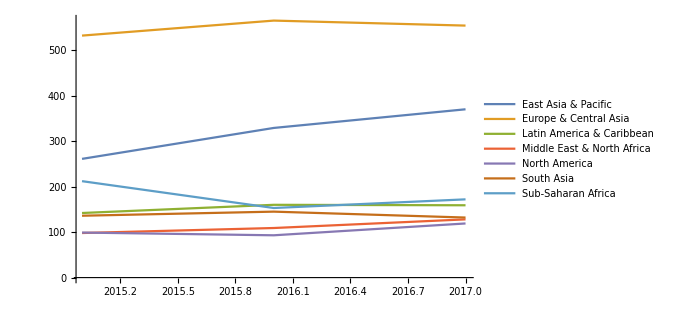

```mathematica
ListLinePlot[Partition[Partition[Riffle[SplitBy[SortBy[studentDataArray[[All,{2,4,5}]],1],{#[[1]],#[[2]]}&][[All,1,2]],Total/@SplitBy[SortBy[studentDataArray[[All,{2,4,5}]],1],{#[[1]],#[[2]]}&][[All,All,3]]],2],3],PlotLegends->DeleteDuplicates[SplitBy[SortBy[studentDataArray[[All,{2,4,5}]],1],{#[[1]],#[[2]]}&][[All,1,1]]],ImageSize->500]
```

## Conclusion

Of course there are many more things that could be analyzed using this or more datasets like the development of the UWC students concentration in a region over time or the historic developments with historic data. For now, I hope, this computational essay provides an impressive visualization for the diversity of UWCs, but also inequalities in student numbers or the distribution of schools.

## Further Explorations

Gender Diversity

Diversity in Religion

Diversity in Ethnicity

Historical Data

## Author contact information

katja.dellalibera@minerva.kgi.edu

## Guidelines for the Author

### Image

Try to use images created in the Wolfram Language as much as possible

If an external image is the only way to go, use Import to get the image into the notebook and reverse close the In/Out cell-group  to hide the input cell.

### Text

Use minimal text in small pieces to explain the topic and transition between pieces of code. One or two lines of text at a time should suffice.

Sub-guideline two

### CodeText

Before each line of code, add a single line in CodeText style, as a lead-in, to say what the code that follows will do.

End this line with a colon

Make a map of Monaco:

```mathematica
GeoGraphics[Entity["Country","Monaco"]]
```

-Graphics-

### Code

Keep code simple and straightforward; code cell should be at most 3 lines long

Breakup complicated lengthy code into multiple segments and separate with CodeText lead-ins explaining each segment

Try to create simple visualizations whenever possible to illustrate the topic and add visual interest

Extra code (for example, visualization options to simply make the output look pretty) can be distracting and take away focus from the main functionality. Either avoid these or use Iconize to hide them.

Instead of

```mathematica
Plot[Sin[x], {x, 1, 10}, PlotStyle -> {Red, Dashed, Thick}]
```

Use

```mathematica
Plot[Sin[x],{x,1,10},]
```

If using a Manipulate, remember to set SaveDefinitions->True, if it refers to definitions not contained within it. This will allow the Manipulate to work without having to re-evaluate the notebook, for every new session.

Include Data Repository

Include Function Repository (mention coming soon)